```mathematica
data=Table[Select[Import["/Users/wanglong/Dropbox/Datas/Nb6Test/bar/"<>ToString@i<>"_nb16.log","Table"],Length@#==6&][[All,2;;6]],{i,0,15}];
```

```mathematica
data2=Table[Select[Import["/Users/wanglong/Dropbox/Datas/Nb6Test/bar/"<>ToString@i<>"_nbngpu16.log","Table"],Length@#==6&][[All,2;;6]],{i,0,15}];
```

```mathematica
data3=Table[Select[Import["/Users/wanglong/Dropbox/Datas/Nb6Test/bar/"<>ToString@i<>"_nb16_2.log","Table"],Length@#==7&][[All,3;;7]],{i,0,15}];
```

```mathematica
data4=Table[Select[Import["/Users/wanglong/Dropbox/Datas/Nb6Test/bar/"<>ToString@i<>"_nb24.log","Table"],Length@#==6&][[All,2;;6]],{i,0,23}];
```

```mathematica
data5=Table[Select[Import["/Users/wanglong/Dropbox/Datas/Nb6Test/bar/"<>ToString@i<>"_nbn16.log","Table"],Length@#==8&][[All,3;;8]],{i,0,15}];
```

```mathematica
Length/@data
```

{30171,25755,26883,25804,25572,25994,27455,27559,26269,25832,25651,26926,25571,25813,26021,25729}

```mathematica
Length /@data2
```

{28434,25717,25689,25652,25450,25574,25590,26563,25934,25771,25622,25449,25667,25579,26605,26484}

```mathematica
Length/@data3
```

{31728,31677,31911,31664,31555,31692,32028,32106,31718,31750,31629,31847,31506,31665,31725,31766}

```mathematica
Length/@data4
```

{32024,26752,28393,26685,25728,25769,25456,26062,25558,25640,25614,25571,25266,25475,25297,25614,25392,26214,25903,25710,25343,25447,26052,25390}

```mathematica
Length/@data5
```

{33197,28656,28527,29074,28650,28569,28635,28602,28916,28439,28556,29141,28478,28792,28434,28435}

```mathematica
frac=Table[Length[Select[data[[i]],#[[4]]<10^j&]],{i,16},{j,-5,1}];
```

```mathematica
frac2=Table[Length[Select[data2[[i]],#[[4]]<10^j&]],{i,16},{j,-5,1}];
```

```mathematica
frac3=Table[Length[Select[data4[[i]],#[[4]]<10^j&]],{i,24},{j,-5,1}];
```

```mathematica
frac5=Table[Length[Select[data5[[i]],#[[4]]<10^j&]],{i,16},{j,-5,1}];
```

```mathematica
ListPlot3D[Flatten[Table[{i,j-6,frac[[i,j]]},{i,16},{j,6}],1]]
```

```mathematica
ListPlot3D[Flatten[Table[{i,j-6,frac2[[i,j]]},{i,16},{j,6}],1]]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j-6,frac3[[i,j]]},{i,24},{j,6}],1]]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j-6,frac5[[i,j]]},{i,16},{j,6}],1]]
```

-Graphics3D-

```mathematica
Table[Length[Select[data2[[i]],#[[4]]<1*^-4&]],{i,16}]
```

{6172,9,0,371,0,32,84,1740,669,567,520,1761,500,77,12892,3132}

```mathematica
Table[Length[Select[data3[[i]],#[[4]]<1*^-4&]],{i,16}]
```

{30032,30052,30240,29915,29578,30286,30413,30828,30253,30200,29476,29608,29304,30107,30010,30181}

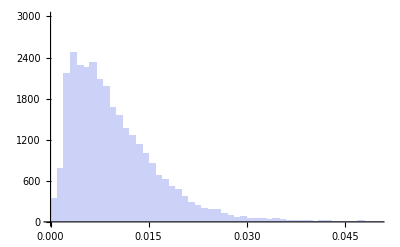
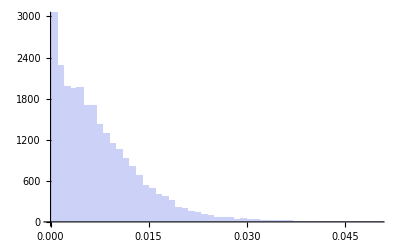
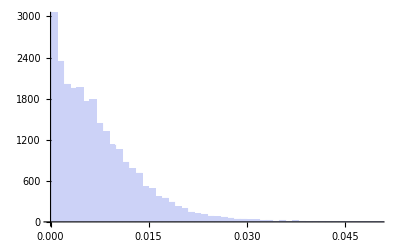
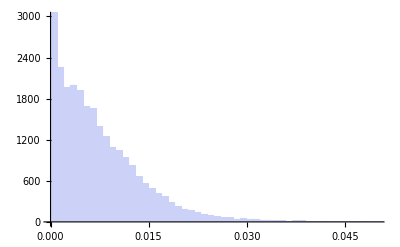
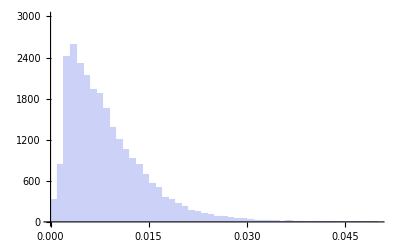
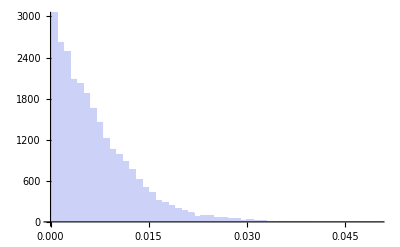
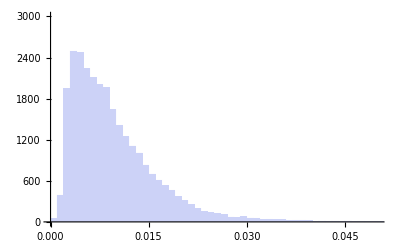
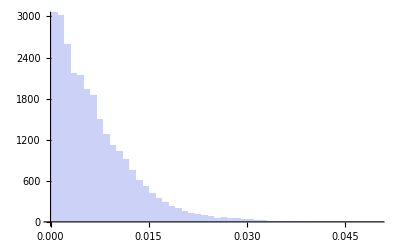

```mathematica
Table[Histogram[data[[i,All,4]],PlotRange->{{0,0.05},{0,3000}}],{i,16}]
```

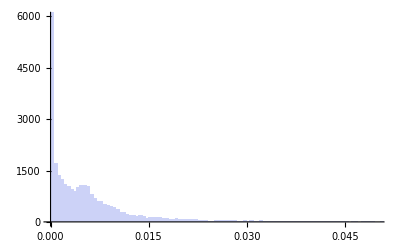
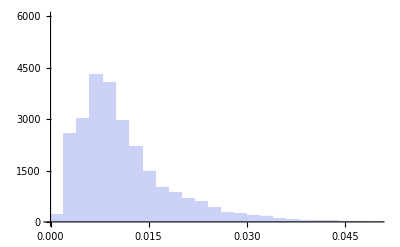
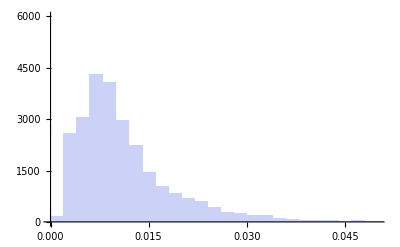
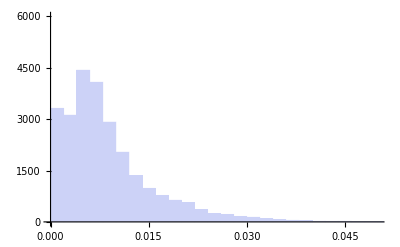
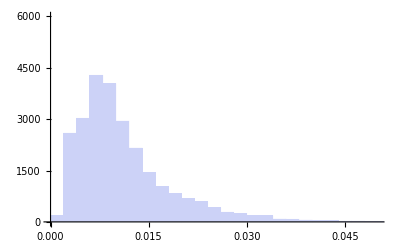
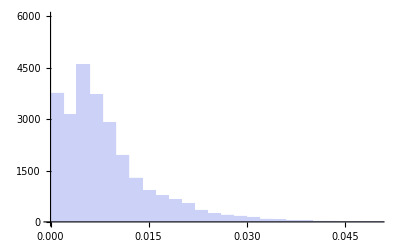
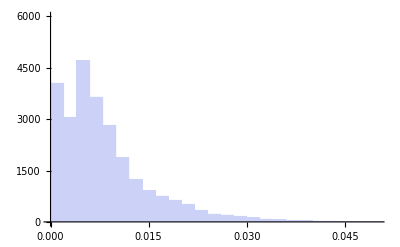
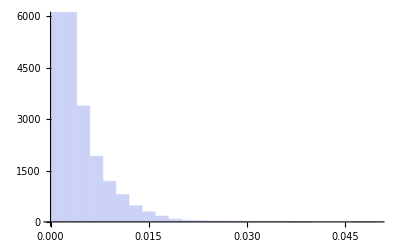

```mathematica
Table[Histogram[data2[[i,All,4]],PlotRange->{{0,0.05},{0,6000}}],{i,16}]
```

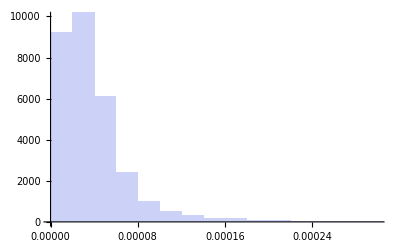
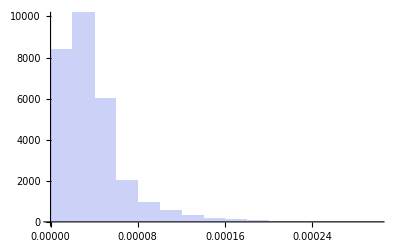
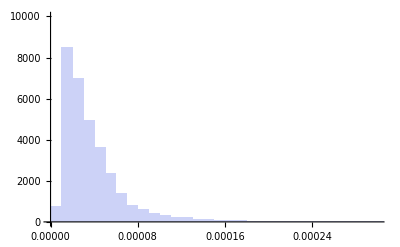
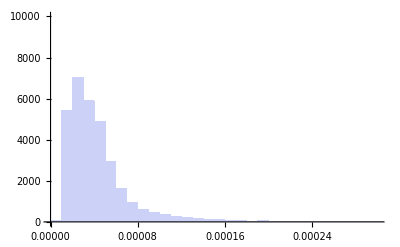
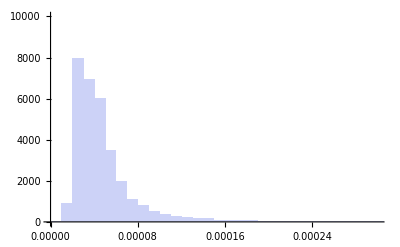
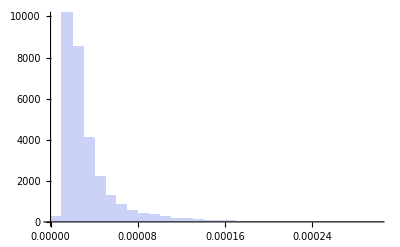
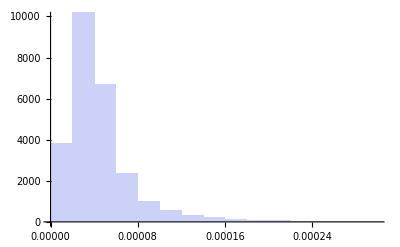
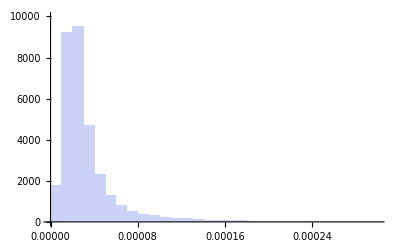

```mathematica
Table[Histogram[data3[[i,All,4]],1000,PlotRange->{{0,0.0003},{0,10000}}],{i,16}]
```

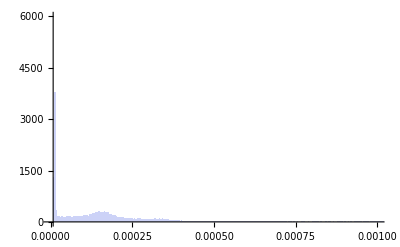
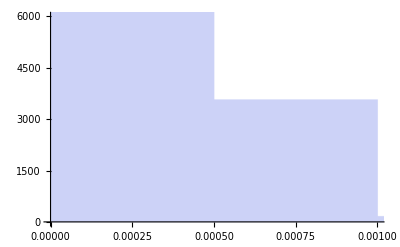
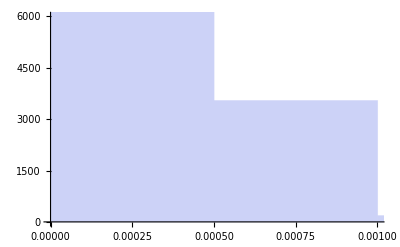
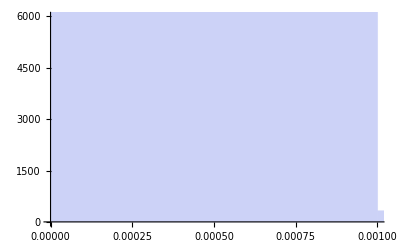
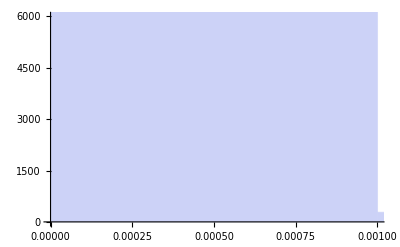
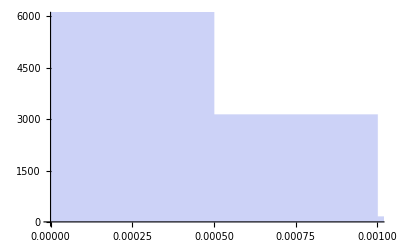
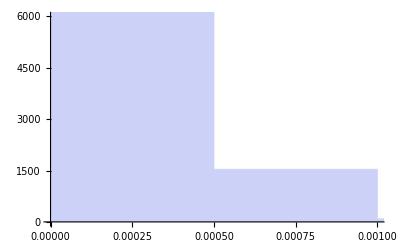
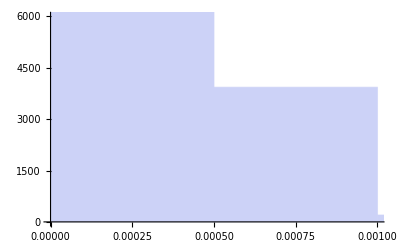

```mathematica
Table[Histogram[data5[[i,All,4]],1000,PlotRange->{{0,0.001},{0,6000}}],{i,16}]
```

```mathematica
Plus@@@data[[All,All,4]]
```

{297.663,193.603,190.383,192.82,223.301,179.488,266.7,186.271,137.337,36.3439,260.719,279.908,265.913,183.384,194.208,190.837}

```mathematica
Plus@@@data2[[All,All,4]]
```

{146.96210145950317,297.481,297.413,228.837,293.726,222.8,219.17,100.287,212.351,213.904,211.657,201.941,213.403,220.472,53.1593,114.564}

```mathematica
ListLogLogPlot[Flatten[Table[{i,data[[i,All,j]]},{j,Length@data[[i]]},{i,Length@data}],1],PlotRange->Full]
```

Part::pspec: Part specification i is neither a machine-sized integer nor a list of machine-sized integers.

-Graphics-

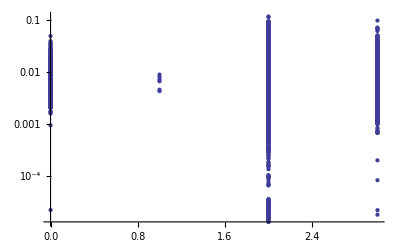

```mathematica
ListLogPlot[data[[1,All,{1,4}]],PlotRange->Full]
```